```mathematica
ClearAll["Global`*"];
```

## The Intertemporal Problem

```mathematica
(*Set parameter values*)
alpha=0.5;(*Preference parameter*)
r=.5;(*rate of interest*)
p=20;(*Price of goods*)
m=1000;(*available hours (24-subsistence)*)
(*Define the utility function*)U[c1_,c2_]:=c1^alpha*c2^(1-alpha)
```

```mathematica
(*Define the Lagrangian*)
Lagrangian[c1_,c2_,lambda_]:=U[c1,c2]+lambda*(m(1+r)+m-p*c1(1+r)-p*c2)
```

```mathematica
(*Set up the first-order conditions*)
eq1=D[Lagrangian[c1,c2,lambda],c1]==0;
eq2=D[Lagrangian[c1,c2,lambda],c2]==0;
eq3=m(1+r)+m-p*c1(1+r)-p*c2==0;
```

```mathematica
(*Solve the system of equations*)
solution=Solve[{eq1,eq2,eq3},{c1,c2,lambda}]
```

{{c1→41.6667,c2→62.5,lambda→0.0204124}}

```mathematica
utilityStar=U[c1/.solution, c2/.solution][[1]];
c1Star=c1/.solution[[1]];
c2Star=c2/.solution[[1]];
sStar=m-c1Star*p;
clearStar=m(1+r)+m-p*c1Star(1+r)-p*c2Star;
List[utilityStar,c1Star,c2Star,sStar,clearStar]
```

{51.031,41.6667,62.5,166.667,0.}

```mathematica
utilityPlot = Plot3D[
U[c1,c2],{c1,0,2*m/p},{c2,0,2m(1+r)/p}
];
optimalBundle3D=Flatten[{c1Star,c2Star,utilityStar}];
optimalPoint3D[a_]:=
Graphics3D[
{Red,Ball[a,5]}
];
```

```mathematica
Show[
utilityPlot,
 optimalPoint3D[optimalBundle3D]
]
```

-Graphics3D-

```mathematica
indiCurves = 
ContourPlot[
U[c1,c2],{c1,0,2m/p},{c2,0,2m(1+r)/p},
Contours->5,
ContourShading->None,
PlotLegends->Automatic,
FrameLabel->{"Consumption in Period 1","Consumption in Period 2"},
PlotLabel->"Indifference Curves and the Worker's Budget Line"
];
```

```mathematica
maxIndiCurve=
ContourPlot[
U[c1,c2]==utilityStar,
{c1,0,2m/p},{c2,0,3*m/p},
ContourStyle->Blue
];
```

```mathematica
budget=
Plot[
m(2+r)/p-c1(1+r),{c1,0,m},
PlotStyle->Directive[Blue,Thick]
];
```

```mathematica
optimalBundle ={c1Star,c2Star}
```

{41.6667,62.5}

```mathematica
optimalPoint[a_]:=
Graphics[
{Red,PointSize[Large],Point[a]}
];
```

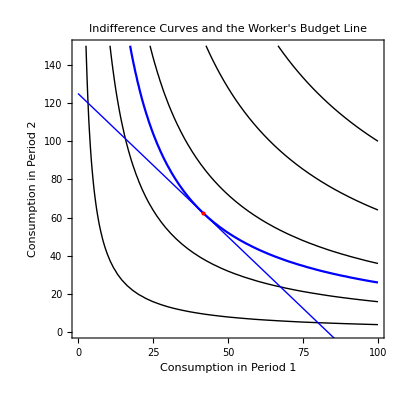

```mathematica
Show[
indiCurves,maxIndiCurve,budget, optimalPoint[optimalBundle]
]
```

```mathematica
Manipulate[Show[]] (*Changing alpha, wage and prices. Use CobbDouglas shortcut*)
```

Manipulate[]